```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,316/2}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,282/2}];
```

```mathematica
largestXRational = 282/2;
largestXIrrational = 316/2;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
dataEnergyPBC=Import["IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100PBC.dat"];
```

```mathematica
dataEnergyOBC=Import["IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100OBC.dat"];
```

Import::nffil: File IrrationalSlope/EigenvaluesParent60DislocationIrrational12to14mP100OBC.dat not found during Import.

```mathematica
dataEnergyPBC;
```

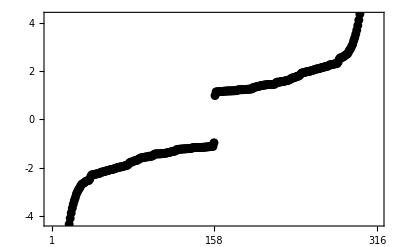

```mathematica
Show[
(** ListPlot[dataEnergyPBC,Frame-> True,Axes-> False,PlotRange-> {{0,2*largestXIrrational},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,largestXIrrational,2*largestXIrrational},None}},BaseStyle-> 18], **)

ListPlot[dataEnergyPBC,PlotStyle-> {Black,PointSize[0.016]},
Frame-> True,Axes-> False,PlotRange-> {{0,2*largestXIrrational},{-4.25,4.25}},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,largestXIrrational,2*largestXIrrational},None}},BaseStyle-> 18]
(** ,

ListPlot[{dataEnergyPBC[[largestXIrrational]]},PlotStyle-> {Red,PointSize[0.018]}] **)
(** ,

Plot[-1.5,{x,210,230},PlotStyle-> {Thick,Red}],
Plot[-3.0,{x,210,230},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{260,-1.5}],Inset["PBC",{260,-3.0}]} **)
]
```

```mathematica
dataEnergyPBC[[largestXIrrational]]
```

{158,-0.976552}

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc,colorfuncBW]
```

```mathematica
dataLDoSPBC=Import["IrrationalSlope/LDOSParent60DislocationIrrational12to14mM005PBC.dat"];
```

```mathematica
dataLDoSPBC;
```

```mathematica
dataLDoSPBCSorted = SortBy[Last][dataLDoSPBC]
```

{{154,0,0.000127988},{150,0,0.000272807},{157,0,0.00029929},{147,0,0.000438623},{143,0,0.000545411},{145,0,0.000735768},{42,0,0.000736341},{29,0,0.000796676},{141,0,0.000876286},{33,0,0.000960205},{46,0,0.000968524},{148,0,0.00102809},{55,0,0.00106423},{137,0,0.00110642},{152,0,0.00116017},{134,0,0.00116794},{130,0,0.00125418},{16,0,0.00125991},{36,0,0.00143857},{59,0,0.00158191},{20,0,0.00162828},{49,0,0.00163214},{132,0,0.00167688},{40,0,0.00172621},{24,0,0.00172815},{27,0,0.00180062},{135,0,0.00192252},{139,0,0.00196788},{128,0,0.00199616},{53,0,0.00213879},{4,0,0.00217544},{121,0,0.0021863},{117,0,0.00221533},{105,0,0.0022158},{124,0,0.00224207},{31,0,0.00224902},{14,0,0.00231867},{118,0,0.00239084},{11,0,0.00239289},{44,0,0.00242576},{7,0,0.0024345},{114,0,0.00258074},{18,0,0.00260478},{101,0,0.00260672},{34,0,0.00265466},{103,0,0.00276849},{62,0,0.00286169},{47,0,0.00288844},{107,0,0.0028903},{119,0,0.00290299},{38,0,0.00301593},{126,0,0.00303327},{122,0,0.00304088},{22,0,0.00309053},{116,0,0.0030953},{111,0,0.00315625},{115,0,0.00320231},{57,0,0.00330748},{100,0,0.00333379},{51,0,0.00337885},{113,0,0.00347658},{120,0,0.00348396},{94,0,0.00350006},{112,0,0.00354202},{2,0,0.00355217},{98,0,0.00360845},{92,0,0.00364603},{104,0,0.00364708},{5,0,0.00368401},{109,0,0.00369396},{9,0,0.00382882},{108,0,0.00384203},{123,0,0.00384775},{96,0,0.00385518},{60,0,0.00398203},{90,0,0.00400328},{131,0,0.00401779},{66,0,0.00403037},{127,0,0.00418358},{106,0,0.00444725},{110,0,0.00446312},{102,0,0.00470836},{129,0,0.00476396},{125,0,0.00483872},{64,0,0.00488983},{17,0,0.00505144},{99,0,0.00515522},{1,0,0.00518556},{88,0,0.00523669},{30,0,0.00528202},{3,0,0.0052902},{87,0,0.00534591},{13,0,0.00534914},{133,0,0.00561189},{43,0,0.00561586},{26,0,0.00565972},{91,0,0.00576203},{6,0,0.00576467},{95,0,0.00583087},{56,0,0.00592983},{10,0,0.00600024},{69,0,0.00611783},{97,0,0.00613917},{15,0,0.00638114},{136,0,0.00642876},{23,0,0.00642932},{19,0,0.00646512},{39,0,0.00651506},{93,0,0.00662326},{35,0,0.00670044},{12,0,0.00672948},{32,0,0.00677961},{52,0,0.00684264},{8,0,0.00684905},{28,0,0.00685709},{48,0,0.00704951},{25,0,0.00714463},{45,0,0.00719395},{140,0,0.00722872},{21,0,0.00731332},{41,0,0.00743088},{89,0,0.00746163},{138,0,0.0076093},{83,0,0.00762283},{37,0,0.00770644},{68,0,0.00777273},{144,0,0.00779413},{58,0,0.00799635},{61,0,0.00801342},{65,0,0.00817176},{54,0,0.00830701},{142,0,0.00834535},{72,0,0.00836799},{50,0,0.00838308},{86,0,0.00927377},{85,0,0.00963318},{146,0,0.0101389},{63,0,0.0103035},{71,0,0.0105345},{73,0,0.0105734},{67,0,0.0111079},{84,0,0.0111558},{149,0,0.0120866},{151,0,0.0129486},{70,0,0.0129955},{76,0,0.0130207},{82,0,0.0135975},{153,0,0.0143671},{74,0,0.0144123},{80,0,0.014695},{155,0,0.0150757},{156,0,0.0168056},{158,0,0.0201903},{79,0,0.0208778},{81,0,0.0214412},{77,0,0.0233515},{75,0,0.0373373},{78,0,0.110001}}

```mathematica
dataLDoSOBC=Import["BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat"];
```

Import::nffil: File BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat not found during Import.

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@dataLDoSPBC[[All,3]]
```

{0,0.110001}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfuncBW[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.1"},{rng[[2]]-10^-3,"2.2"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

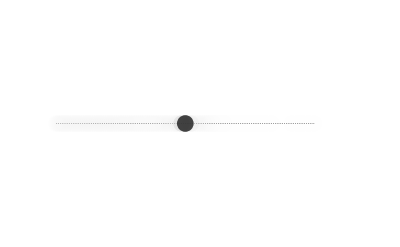

```mathematica
Show[
ListPlot[latticeRational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,Max[Flatten[LatticeIrrational]]+10},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfuncBW[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSPBCSorted,
BaseStyle-> 18
]

]
```